```mathematica
Assuming[A>0&&B>0&&p∈Reals,Maximize[{x^2 A^2+y^2 B^2+2 p x y,Abs[x]+Abs[y]==1},{x,y}]]
```

$Aborted

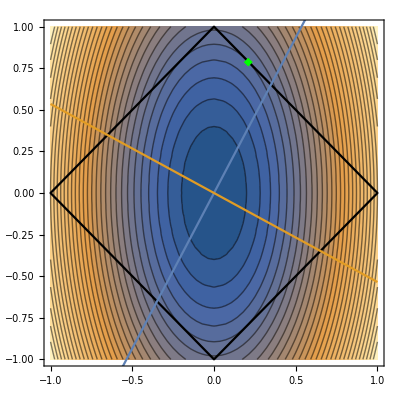

```mathematica
Show[ContourPlot[0.2^2 x^2+0.1^2 y^2+2(0.0) x y,{x,-1,1},{y,-1,1},Contours->30],ContourPlot[Abs[x]+Abs[y]==1,{x,-1,1},{y,-1,1},ContourStyle->Black],Plot[{((0.8816745987679436/0.4718579255320243) x),((0.4718579255320243/-0.8816745987679436)x)},{x,-1,1}],ListPlot[{{0.20961608,0.79038392}},PlotStyle->{Green},PlotMarkers->"◆"]]
```

```mathematica
Eigensystem[{{0.8,0.3},{0.3,1.2}}]
```

{{1.36056,0.639445},{{0.471858,0.881675},{-0.881675,0.471858}}}

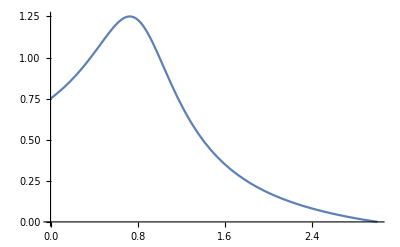

```mathematica
Plot[{(δ 10+(1-δ) 15)/Sqrt[δ^2 10^2+(1-δ)^2 20^2]},{δ,0,3}]
```

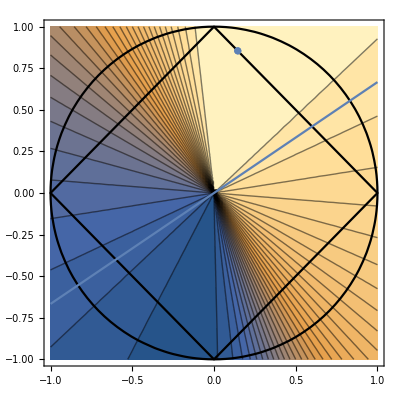

```mathematica
Show[ContourPlot[(x 0.15+y 0.1)/Sqrt[0.2^2 x^2+0.1^2 y^2+2*(0.011)x y],{x,-1,1},{y,-1,1},Contours->30],ContourPlot[Abs[x]+Abs[y]==1,{x,-1,1},{y,-1,1},ContourStyle->Black],ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1},ContourStyle->Black],Plot[((1/1.5) x),{x,-1,1}],ListPlot[{{(1-0.85451752),0.85451752}}]]
```

```mathematica
NMaximize[(x 0.15+y 0.1)/Sqrt[0.2^2 x^2+0.1^2 y^2],{x,y}]
```

{1.25,{x→0.66807,y→1.78152}}

```mathematica
(x 0.15+y 0.1)/Sqrt[0.2^2 x^2+0.1^2 y^2]
```

```mathematica
NMaximize[(δ 10+(1-δ) 15)/Sqrt[δ^2 10^2+(1-δ)^2 20^2],δ]
```

{1.25,{δ→0.727273}}